# Angular Crossing Collimated Flux

## Units + Constants

```mathematica
(*Units*)
MeV=10^6;
keV=10^3;
nC=10^-9;
pC=10^-12;
μJ=10^-6;
nm=10^-9;
mrad=10^-3;
mm=10^-3;
cm=10^-2;
μm=10^-6;
MHz=10^6;
ps=10^-12;
```

```mathematica
(*Constants*)
σT=6.65245871548*10^-29;
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.51099895MeV; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Angles*)
fivedeg=(5*π)/180;
```

## Plotting

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Cases

The optimised values within these cases are using the Compton_Optimisation_Parrallel.nb code, which is outdated (doesn’t include hourglass effect), but is the best for comparing to spectra etc.

```mathematica
CBETA150base={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->1cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.5mrad};
CBETA150opt={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->12.6189cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.43333mrad};

DIANA687base={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.2,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.1mrad};
DIANA687opt={Ee->687MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->0.603575,ϵn->0.5mm mrad,σL->25 μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.09181mrad};

DIANA1519opt={Ee->1519MeV,ϕ->fivedeg,λ->1064nm,Q->100pC,Epulse->100μJ,βIP->1.600,ϵn->0.5mm mrad,σL->25μm,σze->1mm,tpulse->5.7ps,f->100MHz,θcol->0.04269mrad};

pointsource={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->10cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.5mrad};
minpoint={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->10cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.499mrad};
maxpoint={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->10cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.501mrad};

closerpointsource={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->100cm,ϵn->1mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.5mrad};
closerminpoint={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->100cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.499mrad};
closermaxpoint={Ee->150MeV,ϕ->fivedeg,λ->1064nm,Q->32pC,Epulse->62μJ,βIP->100cm,ϵn->0.3mm mrad,σL->25μm,σze->1mm,tpulse->10ps,f->162.5MHz,θcol->0.501mrad};
```

## Integrated Cross Section Calculation

## Intermediaries

```mathematica
(*Scattered photon energy equations*) 
γ[Ee_]:=(Ee+me)/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

## Scattered Photon Energy

```mathematica
Eγ[Ee_,ϕ_,λ_,θ_]:=(EL[λ]*(1+β[Ee]*Cos[ϕ]))/(1-β[Ee]*Cos[θ]+EL[λ]/Ee*(1+Cos[ϕ+θ]));
```

```mathematica
Eγ[Ee,ϕ,λ,0]/.CBETA150opt
```

402516.

## Lorentz Invariants (from Mandelstam Variables)

```mathematica
X[Ee_,ϕ_,λ_]:=(2*γ[Ee]*EL[λ]*(1+β[Ee]*Cos[ϕ]))/me;
Y[Ee_,ϕ_,λ_,θ_]:=(2*γ[Ee]*Eγ[Ee,ϕ,λ,θ]*(1-β[Ee]*Cos[θ]))/me;
```

## Y Angular Variation

```mathematica
YvsθCBETA=Table[{θ/mrad,Y[Ee,0,λ,θ]/.CBETA150opt},{θ,0,1/γ[Ee]/.CBETA150opt,1/(100*γ[Ee])/.CBETA150opt}];
```

```mathematica
YvsθDIANA=Table[{θ/mrad,Y[Ee,0,λ,θ]/.DIANA687opt},{θ,0,1/γ[Ee]/.DIANA687opt,1/(100*γ[Ee])/.DIANA687opt}];
```

```mathematica
CBETAYvsθ=ListLinePlot[YvsθCBETA,Frame->True,FrameLabel->{"Collimation Angle [mrad]","Y" },LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",ImageSize->Medium];
```

```mathematica
DIANAYvsθ=ListLinePlot[YvsθDIANA,Frame->True,FrameLabel->{"Collimation Angle [mrad]","Y" },LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",ImageSize->Medium];
```

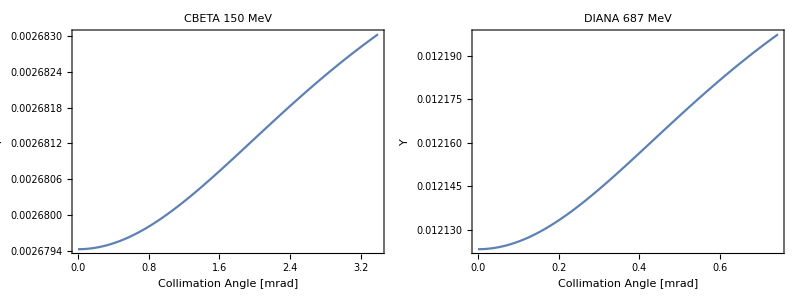

```mathematica
Grid[{{CBETAYvsθ,DIANAYvsθ}}]
```

## Cross Section [Berestetskii, σ = f(Y)]

```mathematica
dσdY[Ee_,ϕ_,λ_,θ_]:=(8*π*re^2)/X[Ee,ϕ,λ]^2*((1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ])^2+1/X[Ee,ϕ,λ]-1/Y[Ee,ϕ,λ,θ]+1/4*(X[Ee,ϕ,λ]/Y[Ee,ϕ,λ,θ]+Y[Ee,ϕ,λ,θ]/X[Ee,ϕ,λ]));
```

## Lorentz Invariant Y Differential [Me, Y = f(θ)]

```mathematica
dYdθ[Ee_,θ_,ϕ_,λ_]:=(X[Ee,ϕ,λ]*β[Ee]*Sin[θ]*(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)-X[Ee,ϕ,λ]*(1-β[Ee]*Cos[θ])*(β[Ee]*Sin[θ]-EL[λ]/Ee*Sin[ϕ+θ]))/(1-β[Ee]*Cos[θ]+(1+Cos[ϕ+θ])*EL[λ]/Ee)^2;
```

## Cross Section [Me, σ = f(θ)]

```mathematica
dσdθ[Ee_,ϕ_,λ_,θ_]:=dσdY[Ee,ϕ,λ,θ]*dYdθ[Ee,θ,ϕ,λ];
```

```mathematica
Off[NIntegrate::nlim,NIntegrate::inumr];
```

```mathematica
σ[Ee_,ϕ_,λ_,θcol_]:=NIntegrate[dσdθ[Ee,ϕ,λ,θ],{θ,0,θcol}];
```

```mathematica
σ[Ee,ϕ,λ,θcol]/.CBETA150base
```

2.08606×10^-30

```mathematica
σ[Ee,ϕ,λ,θcol]/.CBETA150opt
```

1.58358×10^-30

```mathematica
CBETAσvsθ=Table[{θ/mrad,σ[Ee,ϕ,λ,θ]/σT/.CBETA150opt,σ[Ee,ϕ,λ,θ]/σT/.CBETA150base},{θ,-1/γ[Ee]/.CBETA150base,1/γ[Ee]/.CBETA150base,1/(200*γ[Ee])/.CBETA150base}];
```

```mathematica
DIANAσvsθ=Table[{θ/mrad,σ[Ee,ϕ,λ,θ]/σT/.DIANA687opt,σ[Ee,ϕ,λ,θ]/σT/.DIANA687base},{θ,-1/γ[Ee]/.DIANA687base,1/γ[Ee]/.DIANA687base,1/(200*γ[Ee])/.DIANA687base}];
```

```mathematica
baseCBETAσvsθ=ListLinePlot[Partition[Riffle[CBETAσvsθ⟦All,1⟧,CBETAσvsθ⟦All,2⟧],2],Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Int. Cross Section [σ/σ_T]"},ImageSize->Medium];
```

```mathematica
baseDIANAσvsθ=ListLinePlot[Partition[Riffle[DIANAσvsθ⟦All,1⟧,DIANAσvsθ⟦All,2⟧],2],Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Int. Cross Section [σ/σ_T]"},ImageSize->Medium];
```

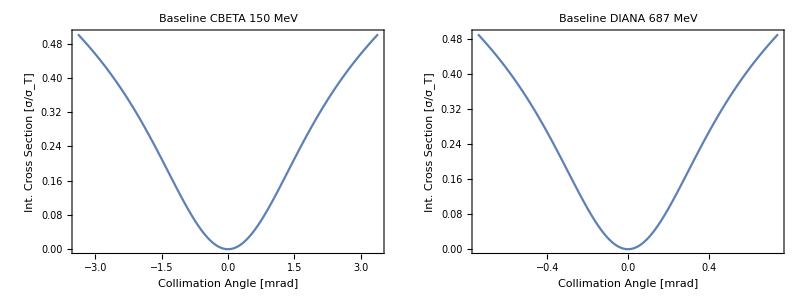

```mathematica
Grid[{{baseCBETAσvsθ,baseDIANAσvsθ}}]
```

## Integrated Cross Section Investigation

## Integrated Cross Section Plots

```mathematica
σvsθCBETA150=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.CBETA150opt)/σT,(σ[Ee,ϕ,λ,θ]/.CBETA150opt)/σT,(σ[Ee,(45*π)/180,λ,θ]/.CBETA150opt)/σT,(σ[Ee,(90*π)/180,λ,θ]/.CBETA150opt)/σT,(σ[Ee,(270*π)/180,λ,θ]/.CBETA150opt)/σT},{θ,-1/γ[Ee]/.CBETA150opt,1/γ[Ee]/.CBETA150opt,1/(100*γ[Ee])/.CBETA150opt}];
```

```mathematica
σvsθDIANA687=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.DIANA687opt)/σT,(σ[Ee,ϕ,λ,θ]/.DIANA687opt)/σT,(σ[Ee,(45*π)/180,λ,θ]/.DIANA687opt)/σT,(σ[Ee,(90*π)/180,λ,θ]/.DIANA687opt)/σT,(σ[Ee,(270*π)/180,λ,θ]/.DIANA687opt)/σT},{θ,-1/γ[Ee]/.DIANA687opt,1/γ[Ee]/.DIANA687opt,1/(100*γ[Ee])/.DIANA687opt}];
```

```mathematica
σvsθDIANA1519=Table[{θ/mrad,(σ[Ee,0,λ,θ]/.DIANA1519opt)/σT,(σ[Ee,ϕ,λ,θ]/.DIANA1519opt)/σT,(σ[Ee,(45*π)/180,λ,θ]/.DIANA1519opt)/σT,(σ[Ee,(90*π)/180,λ,θ]/.DIANA1519opt)/σT,(σ[Ee,(270*π)/180,λ,θ]/.DIANA1519opt)/σT},{θ,-1/γ[Ee]/.DIANA1519opt,1/γ[Ee]/.DIANA1519opt,1/(100*γ[Ee])/.DIANA1519opt}];
```

```mathematica
csCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,2⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,3⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,4⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,5⟧],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,σvsθCBETA150⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

```mathematica
csDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,2⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,3⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,4⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,5⟧],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,σvsθDIANA687⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

```mathematica
csDIANA1519=ListLinePlot[{Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,2⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,3⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,4⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,5⟧],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,σvsθDIANA1519⟦All,6⟧],2]},Frame->True,PlotStyle->{Red,Blue,Orange,Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1519 MeV",FrameLabel->{"Collimation Angle [mrad]","Norm. Int. Cross Section [σ/σ_T]"},PlotLegends->Placed[LineLegend[{"ϕ = 0°","ϕ = 5°","ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.15,0.2}],ImageSize->Large];
```

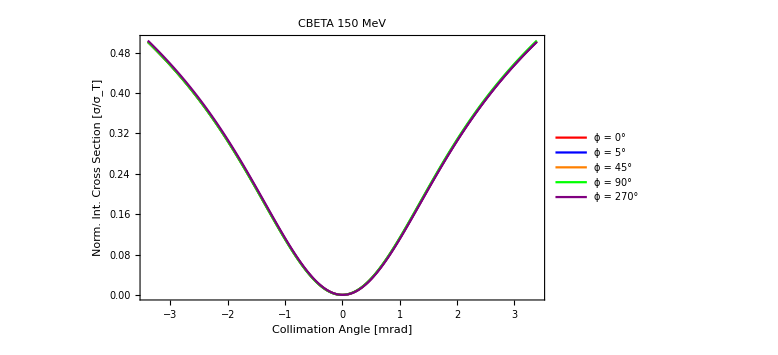
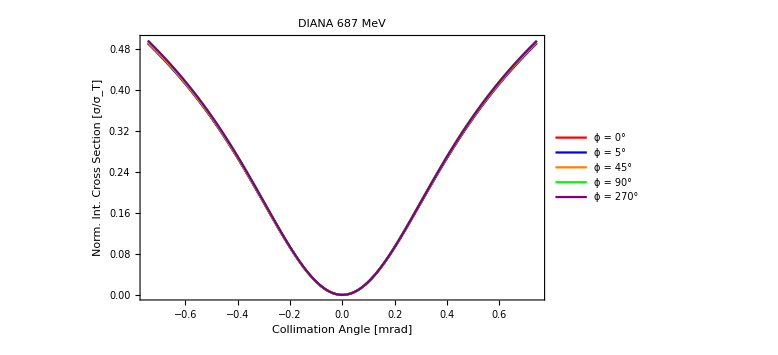
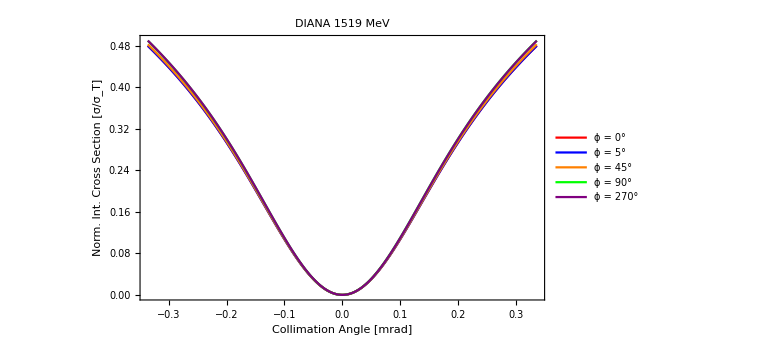
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{{csCBETA150,csDIANA687},{csDIANA1519}}]
```

## Integrated Cross Section Residuals

```mathematica
REScsCBETA150=ListLinePlot[{Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθCBETA150⟦All,1⟧,(σvsθCBETA150⟦All,2⟧-σvsθCBETA150⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"CBETA 150 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T ×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.18,0.45}],ImageSize->Large];
```

```mathematica
REScsDIANA687=ListLinePlot[{Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,4⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,5⟧)*10^3],2],Partition[Riffle[σvsθDIANA687⟦All,1⟧,(σvsθDIANA687⟦All,2⟧-σvsθDIANA687⟦All,6⟧)*10^3],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 687 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T×10^-3]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.4,0.25}],ImageSize->Large];
```

```mathematica
REScsDIANA1519=ListLinePlot[{Partition[Riffle[σvsθDIANA1519⟦All,1⟧,(σvsθDIANA1519⟦All,2⟧-σvsθDIANA1519⟦All,4⟧)*10^2],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,(σvsθDIANA1519⟦All,2⟧-σvsθDIANA1519⟦All,5⟧)*10^2],2],Partition[Riffle[σvsθDIANA1519⟦All,1⟧,(σvsθDIANA1519⟦All,2⟧-σvsθDIANA1519⟦All,6⟧)*10^2],2]},Frame->True,LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"DIANA 1519 MeV",FrameLabel->{"Collimation Angle [mrad]","Residual [(σ (0  °) - σ (ϕ))/σ_T×10^-2]"},PlotLegends->Placed[LineLegend[{"ϕ = 45°","ϕ = 90°","ϕ = 270°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.4,0.25}],ImageSize->Large];
```

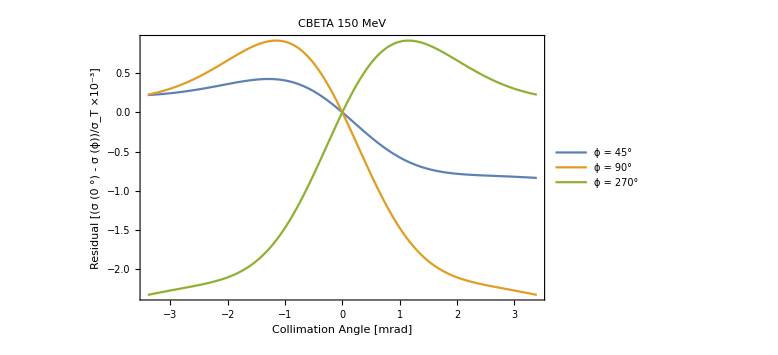
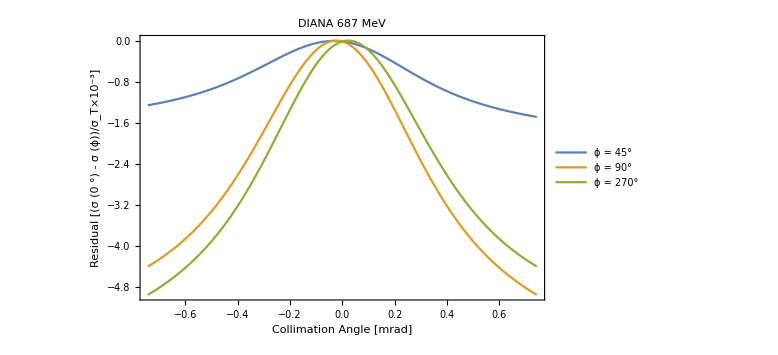
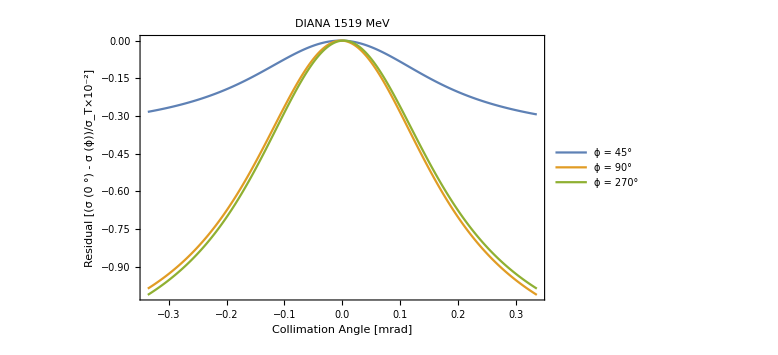
-Graphics- | -Graphics-
-Graphics- |

```mathematica
Grid[{{REScsCBETA150,REScsDIANA687},{REScsDIANA1519}}]
```

## Collimated Flux Calculation [My Method]

## Collimated Flux Intermediaries

```mathematica
(*Luminosity equations*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(elecharge*EL[λ]);
σe[βIP_,ϵn_,Ee_]:=Sqrt[(βIP*ϵn)/γ[Ee]];
σzl[tpulse_]:=clight*tpulse;
convxy[βIP_,ϵn_,Ee_,σL_]:=Sqrt[σe[βIP,ϵn,Ee]^2+σL^2];
convz[σze_,tpulse_]:=Sqrt[σze^2+σzl[tpulse]^2];
```

## Head-on Luminosity

```mathematica
L[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_]:=(Ne[Q]*NL[Epulse,λ])/(2*π*convxy[βIP,ϵn,Ee,σL]^2);
```

## Angular Crossing Luminosity Reduction Factor

```mathematica
RAC[βIP_,ϵn_,Ee_,σL_,ϕ_,σze_,tpulse_]:=(convxy[βIP,ϵn,Ee,σL]*Cos[ϕ])/Sqrt[convxy[βIP,ϵn,Ee,σL]^2*Cos[ϕ]^2+convz[σze,tpulse]^2*Sin[ϕ]^2];
```

## Collimated Flux [Me]

```mathematica
Fcol[Ee_,ϕ_,λ_,θcol_,βIP_,ϵn_,σL_,σze_,tpulse_,Q_,Epulse_,f_]:=σ[Ee,ϕ,λ,θcol]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

```mathematica
Fpoint=Fcol[Ee,ϕ,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.pointsource
```

4.77792×10^8

```mathematica
Fcol[Ee,ϕ,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.minpoint
```

4.75964×10^8

```mathematica
Fcol[Ee,ϕ,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.maxpoint
```

4.79624×10^8

```mathematica
Ftop=((Fcol[Ee,ϕ,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.maxpoint)+(Fcol[Ee,ϕ,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.minpoint))/2
```

4.77794×10^8

```mathematica
(Ftop-Fpoint)/Ftop
```

3.18471×10^-6

## Collimated Flux [My Method] Investigation

## CBETA Flux Cases

```mathematica
FcolCBETA150base=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base},{θ,0,1/γ[Ee]/.CBETA150base,1/(100*γ[Ee])/.CBETA150base}];
```

```mathematica
FcolCBETA150opt=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt},{θ,0,1/γ[Ee]/.CBETA150opt,1/(100*γ[Ee])/.CBETA150opt}];
```

```mathematica
baseFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,2⟧],2],Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,2⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"0.5% BW Optimised CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
zerodegFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,2⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,2⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 0°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
fivedegFcolCBETA=ListLinePlot[{Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,3⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 5°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Optimised","Baseline"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

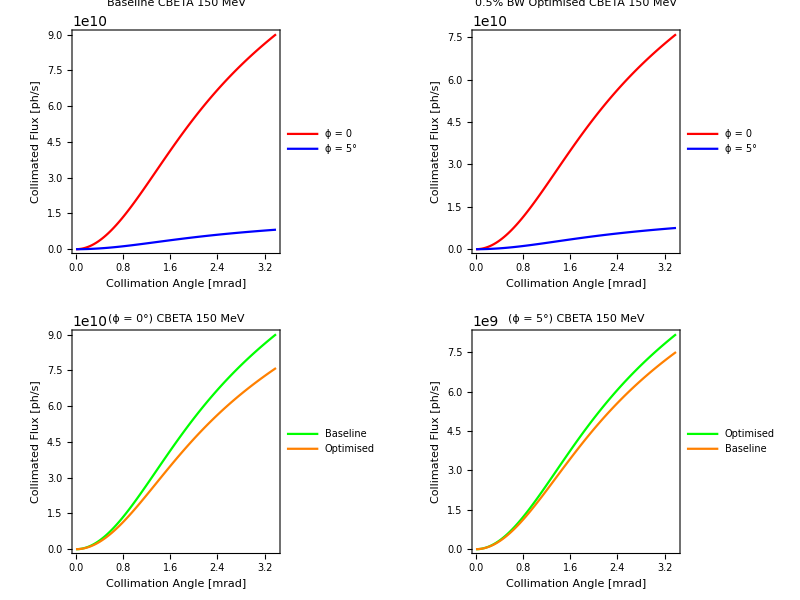

```mathematica
Grid[{{baseFcolCBETA,optFcolCBETA},{zerodegFcolCBETA,fivedegFcolCBETA}}]
```

## DIANA Flux Cases

```mathematica
FcolDIANA687base=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base},{θ,0,1/γ[Ee]/.DIANA687base,1/(100*γ[Ee])/.DIANA687base}];
```

```mathematica
FcolDIANA687opt=Table[{θ/mrad,Fcol[Ee,0,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt,Fcol[Ee,ϕ,λ,θ,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt},{θ,0,1/γ[Ee]/.DIANA687opt,1/(100*γ[Ee])/.DIANA687opt}];
```

```mathematica
baseFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,2⟧],2],Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,2⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,3⟧],2]},PlotStyle->{Red,Blue},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"0.5% BW Optimised DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"ϕ = 0","ϕ = 5°"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
zerodegFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,2⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,2⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 0°) DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Baseline","Optimised"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
fivedegFcolDIANA=ListLinePlot[{Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,3⟧],2]},PlotStyle->{Green,Orange},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"(ϕ = 5°) CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Optimised","Baseline"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

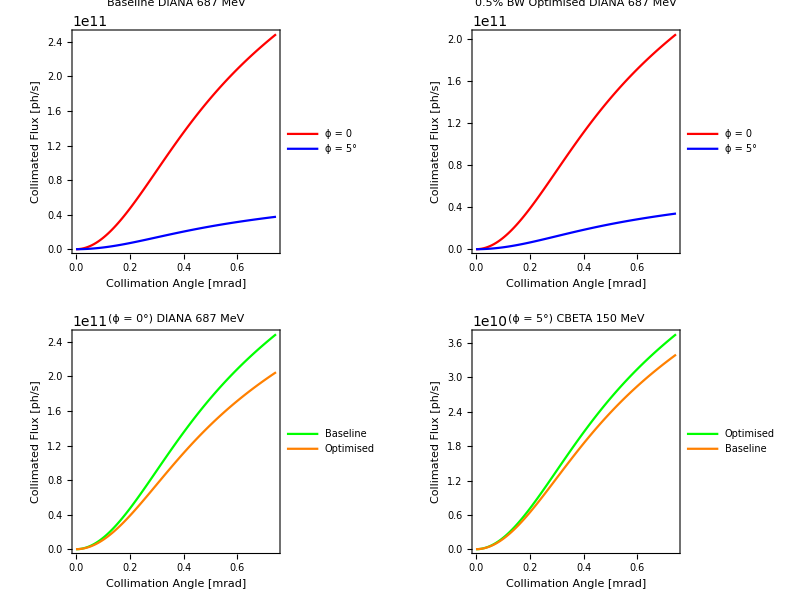

```mathematica
Grid[{{baseFcolDIANA,optFcolDIANA},{zerodegFcolDIANA,fivedegFcolDIANA}}]
```

## Analytical Collimated Flux Comparative Methods

## Collimated Flux Comparative Methods Intermediaries

```mathematica
(*Xrec is the recoil parameter in the head-on, ultra-relativistic case. Used in comparative sources - not mine!*) 
Xrec[Ee_,λ_]:=(4*γ[Ee]*EL[λ])/me;
(*Cross section in the Thomson limit i.e as X->0*)
σc[Ee_,λ_]:=σT*(1-Xrec[Ee,λ]);
(*Rayleigh Range*)
zr[σL_,λ_]:=(4*π*σL^2)/λ;
(*Acceptance angle for Collimation Equations*)
ψ[Ee_,θ_]:=γ[Ee]*θ;
```

## Krafft F_(0.1%) Method

```mathematica
F01[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_,ϕ_,σze_,tpulse_]:=1.5*10^-3*σc[Ee,λ]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f;
```

## Curatolo F_ψ Method

```mathematica
FψCuratolo[Ee_,λ_,Q_,Epulse_,βIP_,ϵn_,σL_,f_,θ_,ϕ_,σze_,tpulse_]:=σc[Ee,λ]*RAC[βIP,ϵn,Ee,σL,ϕ,σze,tpulse]*L[Ee,λ,Q,Epulse,βIP,ϵn,σL]*f*((1+(CubeRoot[Xrec[Ee,λ]]*ψ[Ee,θ]^2)/3)*ψ[Ee,θ]^2)/((1+(1+Xrec[Ee,λ]/2)ψ[Ee,θ]^2)*(1+ψ[Ee,θ]^2));
```

## Curatolo vs My Method

```mathematica
FψCBETA=Table[{θ/mrad,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.CBETA150opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.CBETA150base},{θ,0,1/γ[Ee]/.CBETA150base,1/(100*γ[Ee])/.CBETA150base}];
```

```mathematica
FψDIANA=Table[{θ/mrad,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.DIANA687opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θ,ϕ,σze,tpulse]/.DIANA687base},{θ,0,1/γ[Ee]/.DIANA687base,1/(100*γ[Ee])/.DIANA687base}];
```

```mathematica
baseCBETAFψvsFcol=ListLinePlot[{Partition[Riffle[FψCBETA⟦All,1⟧,FψCBETA⟦All,3⟧],2],Partition[Riffle[FcolCBETA150base⟦All,1⟧,FcolCBETA150base⟦All,3⟧],2]},PlotStyle->{Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optCBETAFψvsFcol=ListLinePlot[{Partition[Riffle[FψCBETA⟦All,1⟧,FψCBETA⟦All,2⟧],2],Partition[Riffle[FcolCBETA150opt⟦All,1⟧,FcolCBETA150opt⟦All,3⟧],2]},PlotStyle->{Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Optimised CBETA 150 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
baseDIANAFψvsFcol=ListLinePlot[{Partition[Riffle[FψDIANA⟦All,1⟧,FψDIANA⟦All,3⟧],2],Partition[Riffle[FcolDIANA687base⟦All,1⟧,FcolDIANA687base⟦All,3⟧],2]},PlotStyle->{Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Baseline DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

```mathematica
optDIANAFψvsFcol=ListLinePlot[{Partition[Riffle[FψDIANA⟦All,1⟧,FψDIANA⟦All,2⟧],2],Partition[Riffle[FcolDIANA687opt⟦All,1⟧,FcolDIANA687opt⟦All,3⟧],2]},PlotStyle->{Green,Purple},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLabel->"Optimised DIANA 687 MeV",Frame->True,FrameLabel->{"Collimation Angle [mrad]","Collimated Flux [ph/s]"},PlotLegends->Placed[LineLegend[{"Curatolo","Me"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.2,0.7}],ImageSize->Medium];
```

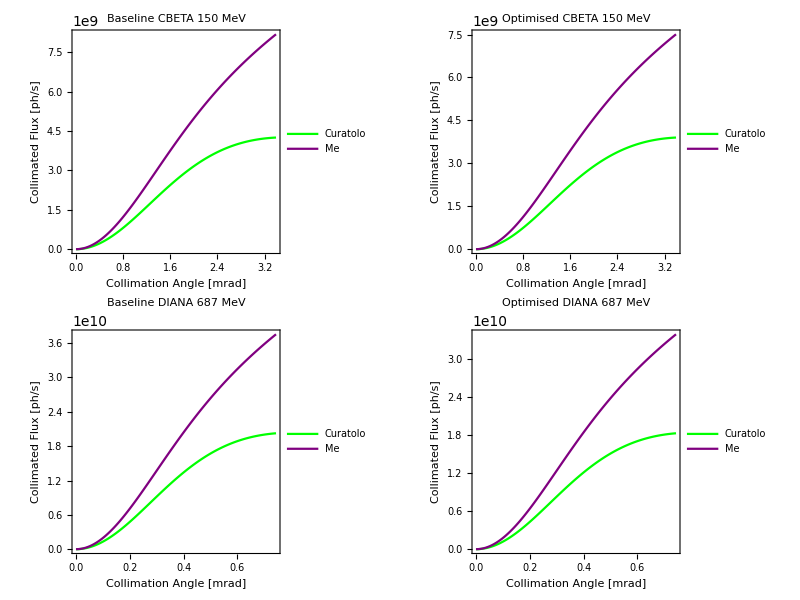

```mathematica
Grid[{{baseCBETAFψvsFcol,optCBETAFψvsFcol},{baseDIANAFψvsFcol,optDIANAFψvsFcol}}]
```

## Semi-Analytical Code Collimated Flux Comparative Methods

## ICARUS Integrated Flux

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA"];
CBETA150N200M=<<"CBETA150_200mil.txt";
CBETA150BASEN20M=<<"CBETA150BASE0.5mrad_20M.txt";
```

Note that the ICARUS data here isn’t exactly optimised for the head-on case , it is for a 5° crossing angle.

```mathematica
CBETAoptICARUSIntFlux=Integrate[Interpolation[CBETA150N200M][x],{x,Min[CBETA150N200M⟦All,1⟧],Max[CBETA150N200M⟦All,1⟧]}]*f*Q/nC/.CBETA150opt
```

3.45231×10^9

```mathematica
CBETAbaseICARUSIntFlux=Integrate[Interpolation[CBETA150BASEN20M][x],{x,Min[CBETA150BASEN20M⟦All,1⟧],Max[CBETA150BASEN20M⟦All,1⟧]}]*f*Q/nC/.CBETA150base
```

4.93189×10^9

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA/7MeV_15MVm"];
DIANA687N100M=<<"DIANA687_100M.txt";
DIANA687BASEN20M=<<"../DIANA687BASE0.1mrad_20M.txt";
```

```mathematica
DIANAoptICARUSIntFlux=Integrate[Interpolation[DIANA687N100M][x],{x,Min[DIANA687N100M⟦All,1⟧],Max[DIANA687N100M⟦All,1⟧]}]*f*Q/nC/.DIANA687opt
```

8.75747×10^9

```mathematica
DIANAbaseICARUSIntFlux=Integrate[Interpolation[DIANA687BASEN20M][x],{x,Min[DIANA687BASEN20M⟦All,1⟧],Max[DIANA687BASEN20M⟦All,1⟧]}]*f*Q/nC/.DIANA687base
```

1.2219×10^10

## ICCS3D Integrated Flux - [NEED TO ASK BALSA TO DO A DIANA 687 MeV RUN]

Note that the ICCS3D data here isn’t exactly optimised for the head-on case , it is for a 5° crossing angle.

```mathematica
rawdataCBETA=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/CBETA/CBETA150_ICCS3D_FINAL.txt","Words"];
ndataCBETA=Length[rawdataCBETA];
ncolumnsCBETA=6;
ndatCBETA=ndataCBETA/ncolumnsCBETA;
BalsaICCSCBETA=Array[Ω,{2,ndatCBETA}];
For[i=0,i<(ndatCBETA+1),i++,
(*for energy*)
Ω[1,i]=Interpreter["Number"][ToString[rawdataCBETA⟦1+ncolumnsCBETA*(i-1)⟧]]*1/keV;
(*for specden*)
Ω[2,i]=Interpreter["Number"][ToString[rawdataCBETA⟦3+ncolumnsCBETA*(i-1)⟧]]*(keV*nC)/elecharge;
];
BalsaValsCBETA=Array[Υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCSCBETA]]+1,i++,
If[BalsaICCSCBETA⟦2,i⟧>10^-20,
AppendTo[BalsaValsCBETA⟦1⟧,BalsaICCSCBETA⟦1,i⟧];
AppendTo[BalsaValsCBETA⟦2⟧,BalsaICCSCBETA⟦2,i⟧];
];
];
```

```mathematica
BalsaValsCBETA=Transpose[BalsaValsCBETA];
```

```mathematica
CBETAoptICCS3DIntFlux=Integrate[Interpolation[BalsaValsCBETA][x],{x,Min[BalsaValsCBETA⟦All,1⟧],Max[BalsaValsCBETA⟦All,1⟧]}]*f*Q/nC/.CBETA150opt
```

3.57972×10^9

Note that the ICCS3D data here is optimised for the head-on case , not for a 5° crossing angle. The factor of 10 is introduced as Balsa needed this in order to correctly + quickly simulate the laser pulse.

```mathematica
rawdataDIANA=Import["C:/Users/user/Documents/Wolfram Mathematica/ICARUS_data/DIANA/DIANA687_ICCS3D.txt","Words"];
ndataDIANA=Length[rawdataDIANA];
ncolumnsDIANA=6;
ndatDIANA=ndataDIANA/ncolumnsDIANA;
BalsaICCSDIANA=Array[η,{2,ndatDIANA}];
For[i=0,i<(ndatDIANA+1),i++,
(*for energy*)
η[1,i]=Interpreter["Number"][ToString[rawdataDIANA⟦1+ncolumnsDIANA*(i-1)⟧]]*1/MeV;
(*for specden*)
η[2,i]=Interpreter["Number"][ToString[rawdataDIANA⟦3+ncolumnsDIANA*(i-1)⟧]]*10*(MeV*nC)/elecharge;
];
BalsaValsDIANA=Array[υ,{2,0}];
For[i=1,i<Length[Transpose[BalsaICCSDIANA]]+1,i++,
If[BalsaICCSDIANA⟦2,i⟧>10^-20,
AppendTo[BalsaValsDIANA⟦1⟧,BalsaICCSDIANA⟦1,i⟧];
AppendTo[BalsaValsDIANA⟦2⟧,BalsaICCSDIANA⟦2,i⟧];
];
];
```

```mathematica
BalsaValsDIANA=Transpose[BalsaValsDIANA];
```

```mathematica
DIANAoptICCS3DIntFlux=Integrate[Interpolation[BalsaValsDIANA][x],{x,Min[BalsaValsDIANA⟦All,1⟧],Max[BalsaValsDIANA⟦All,1⟧]}]*f*Q/nC/.DIANA687opt
```

9.08257×10^9

## Code (ICARUS + ICCS3D) Plots (CBETA + DIANA)

```mathematica
CBETAoptPLOT=ListLinePlot[{CBETA150N200M,BalsaValsCBETA},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"CBETA 150 MeV Optimised",FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{388,405},{0,110}},ImageSize->Medium];
CBETAbasePLOT=ListLinePlot[CBETA150BASEN20M,PlotStyle->{Red},Frame->True,PlotLabel->"CBETA 150 MeV Baseline (θ_col = 0.5 mrad)",FrameLabel->{"Scattered Photon Energy [keV]","Spectral Density [ph/(keV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},ImageSize->Medium];
```

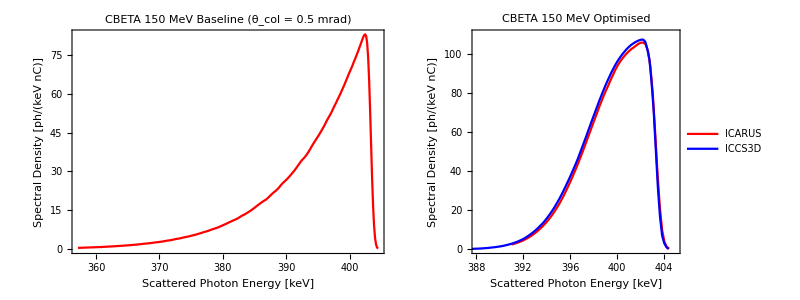

```mathematica
Grid[{{CBETAbasePLOT,CBETAoptPLOT}}]
```

```mathematica
DIANAoptPLOT=ListLinePlot[{DIANA687N100M,BalsaValsDIANA},PlotStyle->{Red,Blue},Frame->True,PlotLabel->"DIANA 687 MeV Optimised",FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotLegends->Placed[LineLegend[{"ICARUS","ICCS3D"},LabelStyle->{12,FontFamily->"Calibri",FontColor->Black},LegendFunction->frame],{0.3,0.8}],PlotRange->{{8,8.37},{0,7000}},ImageSize->Medium];
DIANAbasePLOT=ListLinePlot[DIANA687BASEN20M,PlotStyle->{Red},Frame->True,PlotLabel->"DIANA 687 MeV Baseline (θ_col = 0.1 mrad)",FrameLabel->{"Scattered Photon Energy [MeV]","Spectral Density [ph/(MeV nC)]"},LabelStyle->{15,FontFamily->"Calibri",FontColor->Black},PlotRange->{{7.7,8.4},{0,8000}},ImageSize->Medium];
```

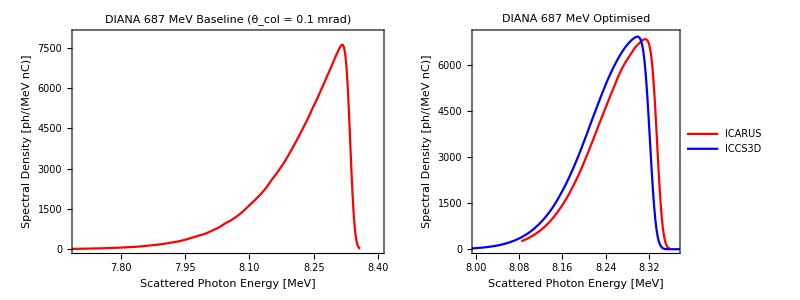

```mathematica
Grid[{{DIANAbasePLOT,DIANAoptPLOT}}]
```

## Comparative Table

This is the comparative table of methods for the collimated flux calculations and their differences. These are all calculated head-on as the codes don’t take into account any angular crossing variation as of yet. The Krafft calculation is done via F_(0.5%) ≃ 5 F_(0.1%) which is a good approximation.

```mathematica
Grid[{{"CBETA 150 MeV Fluxes",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"CBETA 150 MeV Flux Differences",SpanFromLeft,SpanFromLeft},{"Flux Case","Sun Integral","Curatolo Analytical","Krafft Analytical","ICCS3D","ICARUS","Units","F_SUN/F_CURATOLO","F_SUN/F_KRAFFT","F_CURATOLO/F_KRAFFT","F_SUN/F_ICCS3d","F_SUN/F_ICARUS"},{"0.5% BW Optimised",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150opt,5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.CBETA150opt,CBETAoptICCS3DIntFlux,CBETAoptICARUSIntFlux,"ph/s",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150opt,Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse])/.CBETA150opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse])/.CBETA150opt,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt)/CBETAoptICCS3DIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150opt)/CBETAoptICARUSIntFlux},{"Baseline",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150base, "-","-",CBETAbaseICARUSIntFlux,"ph/s",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.CBETA150base,"-","-","-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.CBETA150base)/CBETAbaseICARUSIntFlux},{"DIANA 687 MeV Fluxes",SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,SpanFromLeft,"DIANA 687 MeV Flux Differences",SpanFromLeft,SpanFromLeft},{"Flux Case","Sun Integral","Curatolo Analytical","Krafft Analytical","ICCS3D","ICARUS","Units","F_SUN/F_CURATOLO","F_SUN/F_KRAFFT","F_CURATOLO/F_KRAFFT","F_SUN/F_ICCS3D","F_SUN/F_ICARUS"},{"0.5% BW Optimised",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687opt,5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse]/.DIANA687opt,DIANAoptICCS3DIntFlux,DIANAoptICARUSIntFlux,"ph/s",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687opt,Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse])/.DIANA687opt,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/(5*F01[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,0,σze,tpulse])/.DIANA687opt,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt)/DIANAoptICCS3DIntFlux,(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687opt)/DIANAoptICARUSIntFlux},{"Baseline",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base,FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687base, "-","-",DIANAbaseICARUSIntFlux,"ph/s",Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/FψCuratolo[Ee,λ,Q,Epulse,βIP,ϵn,σL,f,θcol,0,σze,tpulse]/.DIANA687base,"-","-","-",(Fcol[Ee,0,λ,θcol,βIP,ϵn,σL,σze,tpulse,Q,Epulse,f]/.DIANA687base)/DIANAbaseICARUSIntFlux}},Dividers->{{True,True,True,True,True,True,True,True,True,True,True,True,True},{True,True,True,False,True,True,True,False,True}}]
```

CBETA 150 MeV Fluxes |  |  |  |  |  |  | CBETA 150 MeV Flux Differences |  |  |  | 
Flux Case | Sun Integral | Curatolo Analytical | Krafft Analytical | ICCS3D | ICARUS | Units | F_SUN/F_CURATOLO | F_SUN/F_KRAFFT | F_CURATOLO/F_KRAFFT | F_SUN/F_ICCS3d | F_SUN/F_ICARUS
0.5% BW Optimised | 3.6009×10^9 | 2.38398×10^9 | 1.13278×10^9 | 3.57972×10^9 | 3.45231×10^9 | ph/s | 1.51046 | 3.1788 | 2.10453 | 1.00592 | 1.04304
Baseline | 5.62815×10^9 | 3.72655×10^9 | - | - | 4.93189×10^9 | ph/s | 1.51028 | - | - | - | 1.14118
DIANA 687 MeV Fluxes |  |  |  |  |  |  | DIANA 687 MeV Flux Differences |  |  |  | 
Flux Case | Sun Integral | Curatolo Analytical | Krafft Analytical | ICCS3D | ICARUS | Units | F_SUN/F_CURATOLO | F_SUN/F_KRAFFT | F_CURATOLO/F_KRAFFT | F_SUN/F_ICCS3D | F_SUN/F_ICARUS
0.5% BW Optimised | 9.05462×10^9 | 6.10023×10^9 | 3.0874×10^9 | 9.08257×10^9 | 8.75747×10^9 | ph/s | 1.48431 | 2.93277 | 1.97585 | 0.996923 | 1.03393
Baseline | 1.29744×10^10 | 8.74197×10^9 | - | - | 1.2219×10^10 | ph/s | 1.48415 | - | - | - | 1.06182

Explanations + Reasons for Discrepancies + Caveats
The explanation + derivation of the Sun/Me method of calculating collimated flux from Beresteskii/Sun is in a tex file named CollimatedFluxDerrivation.
• ICARUS vs ICCS3D CBETA 150 MeV yield differences could be due to differing polarisations (linear vs circular/unpolarized) in spectrum (v. small effect), or that ICARUS doesn’t simulate to zero spectral density (more likely).
• Both ICCS3D and ICARUS spectra is for 5° crossing angle optimisation parameters, whereas the new collimated flux calculation is for the new (barely changed) optimisation. This may explain the Sun/Me collimated flux vs codes, although unlikely (v. small changes to optimisations, 3rd sig fig in β functions of CBETA + DIANA case, no change to collimation angle).  
• ICARUS vs ICCS3D DIANA 687 MeV spectra clearly are of different energy ranges as Balsa’s code took in a 687 MeV kinetic as a total energy.
• The variation in difference between the baseline cases of the Sun/Me calculation vs the ICARUS simulation for CBETA (12.7%) and DIANA (5.9%) could be an emittance effect. For CBETA the β* function differs by a factor of ~12, compared to a factor of ~3 in the DIANA case, energy spread effects (beam + laser) are the same, the collimation should be accounted for. So, we would expect to see a greater discrepancy on the CBETA F_SUN/F_ICARUS which is what we see.
• The discrepancy between the codes, the Sun/Me method and the Krafft method could be some kind of normalisation issue. The F_SUN/F_KRAFFT for CBETA is so close to π that this feels like it makes sense, however for the DIANA case this seems a lot less clear. 
• Curatolo’s calculation seems to track the Sun/Me calculation and the codes fairly well. However, we seem to have a constant discrepancy of ~3/2 + potentially a second order recoil effect that has been neglected.